Changed for Mathematica 7     07 - 27 - 2010
Apparently needed no changes for Mathematica 10  11-21-2015

```mathematica
DateSequence[date_,WantTime_]:=If[WantTime=="yes",Row[{date⟦2⟧,"-",date⟦3⟧,"-",date⟦1⟧," ",date⟦4⟧,":",date⟦5⟧}],Row[{date⟦2⟧,"-",date⟦3⟧,"-",date⟦1⟧}]];
DateSequence[DateList[],"no"]
```

8-9-2017

```mathematica
sind[t_]:=Sin[t Degree];
cosd[t_]:=Cos[t Degree];
tand[t_]:=Tan[t Degree];
cotd[t_]:=Cot[t Degree];
secd[t_]:=Sec[t Degree];
cscd[t_]:=Csc[t Degree];
arccosd[t_]:=ArcCos[t]/Degree;
arcsind[t_]:=ArcSin[t]/Degree;
arctand[t_]:=ArcTan[t]/Degree;
length[v_]:=√(v.v);
unit[v_]:=v/length[v];                
Unit[v_]:=v/length[v];  
angle[u_,v_]       :=N[arccosd[u.v/(length[u] length[v])]];
angle[Apt_,Bpt_,Cpt_]:=angle[Apt-Bpt,Cpt-Bpt];
signedangle[a_,b_,nor_]:=If[EqualNumbers[angle[a,b],180.],180.,If[Det[{a,b,nor}]>=0,angle[a,b],-angle[a,b]]];
SignedAngle[a_,b_,nor_]:=If[EqualNumbers[Angle[a,b],π],π,If[Det[{a,b,nor}]>=0,Angle[a,b],-Angle[a,b]]];
SignedAngle[a_,b_,nor_]:=If[Det[{a,b,nor}]>=0,Angle[a,b],-Angle[a,b]]; (* Decide what you want here *)   
Angle[u_,v_]:=Chop[ArcCos[u.v/(length[u] length[v])],10^(-5)];                     
                       (*Chop for case where u and v are parallel. May be dangerous though*)
Angle[u_,v_]:=ArcCos[(u.v)/(length[u] length[v])];    (* Choose one. This used to be AngleRad *)   
area[rect_]:=length[Cross[rect[[2]]-rect[[1]],rect[[4]]-rect[[1]]]];
ScalarProj[a_,b_]:=a.b/length[b];
VectorProj[a_,b_]:=(a.b)/(b.b)b;
PlaneProj[a_,normal_]:=a-VectorProj[a,normal];
RightAngle[a_,b_,c_,scale_]:={b+scale*unit[a-b],b+scale*unit[a-b]+scale*unit[c-b],b+scale*unit[c-b]};
XRot[t_]:=({{1, 0, 0}, {0, Cos[t], -Sin[t]}, {0, Sin[t], Cos[t]}});
YRot[t_]:=({{Cos[t], 0, Sin[t]}, {0, 1, 0}, {-Sin[t], 0, Cos[t]}});
ZRot[t_]:=({{Cos[t], -Sin[t], 0}, {Sin[t], Cos[t], 0}, {0, 0, 1}});
xrot[t_]:=XRot[t Degree];
yrot[t_]:=YRot[t Degree];
zrot[t_]:=ZRot[t Degree];
rot111=({{0, 0, 1}, {1, 0, 0}, {0, 1, 0}});
RotMatrixQ[{w_,{x_,y_,z_}}]:=({{w^2+x^2-y^2-z^2, 2(x y-w z), 2(x z+w y)}, {2(x y+w z), w^2-x^2+y^2-z^2, 2(y z-w x)}, {2(x z-w y), 2(y z+w x), w^2-x^2-y^2+z^2}}) ;              (* Used to be RotMatrix2.  Quaternion {w,{x,y,z}} must have length one *)
rot[ξ_,v_]:=RotMatrixQ[{cosd[ξ/2],sind[ξ/2]unit[v]}];
ROT[v_]:=RotMatrixQ[{√(1-v.v),v}];
ROT[ξ_,v_]:=RotMatrixQ[{Cos[ξ/2],Sin[ξ/2] v/(√(v.v))}];
(*rot[ξ_,v_]:=Transpose[vertical[v]].zrot[ξ].vertical[v];  old, but the two rots are equivalent *)
xref=DiagonalMatrix[{-1,1,1}];
yref=DiagonalMatrix[{1,-1,1}];
zref=DiagonalMatrix[{1,1,-1}];
RefWithUnitNormal[{u_,v_,w_}]:=({{1-2 u^2, -2u v, -2u w}, {-2u v, 1-2 v^2, -2v w}, {-2u w, -2v w, 1-2 w^2}});     (* changed 'Reflection' to 'Ref' April 2012 *)
RefWithUnitNormal[{u_,v_}]:=({{1-2 u^2, -2u v}, {-2u v, 1-2 v^2}});              (* changed 'Reflection' to 'Ref' April 2012; added 2D March 2016 *)
id=IdentityMatrix[3];
Rot2D[t_]:=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}});
rot2d[t_]:=Rot2D[t Degree];
ROTe3e1toOrthonormalv3v1[v3_,v1_]:=Transpose[{v1,Cross[v3,v1],v3}]    (* v3 and v1 must be orthonormal *)
sign[x_]:=If[x<0,-1,1];
xyztp[{θ_,ϕ_}]:={cosd[θ] sind[ϕ],sind[θ] sind[ϕ],cosd[ϕ]};
xyzTP[{t_,p_}]:={Cos[t] Sin[p],Sin[t] Sin[p],Cos[p]};
phi[{x_,y_,z_}]:=arccosd[z/(√(x^2+y^2+z^2))];
Phi[{x_,y_,z_}]:=ArcCos[z/(√(x^2+y^2+z^2))];
theta[{x_,y_,z_}]:=If[√(x^2+y^2)==0,0,               
If[x≥0,arcsind[y/(√(x^2+y^2))],
If[y>=0,180-arcsind[y/(√(x^2+y^2))],
				           -180-arcsind[y/(√(x^2+y^2))]]]];   (* changed Feb 2009 also eliminated carets *)
Theta[{x_,y_,z_}]:=If[√(x^2+y^2)==0,0,               
If[y≥0,ArcCos[x/(√(x^2+y^2))],-ArcCos[x/(√(x^2+y^2))]]];  (* θ in radians, from -π to π; used for lune coordinates *)
theta2d[v_]:=theta[Append[v,0]];
phitheta[v_]:={phi[v],theta[v]};
vertical[p_]:=zrot[theta[p]].yrot[-phi[p]].zrot[-theta[p]]; (* Changed Aug 2002 *)
vertical[a_,b_]:=zrot[-theta[vertical[a].b]].vertical[a]; (* makes a vertical and gives b a theta coordinate of zero *)
verticalViaXAxis[p_]:=yrot[-phi[p]].zrot[-theta[p]]; (* Changed Aug 2002 *)
range[domain_,f_]:=Union[f/@domain];
ListComplement[universe_,set_]:=Select[universe,!MemberQ[set,#]&];  (*Mathematica Complement no good for lists *)
partition[set_,r_]:=(part={};remaining=set;
     While[remaining!={},
	   EqCl=Select[remaining,r[First[remaining],#] &];
		part=Join[part,{EqCl}];
		remaining=ListComplement[remaining,EqCl]];part);
QuotientTopology[domain_,f_]:=(Rangef=range[domain,f];
		Clear[EqCl];
		EqCl[RangeValue_]:={};
		Do[EqCl[f[domain[[i]]]]=Join[EqCl[f[domain[[i]]]],{domain[[i]]}],{i,Length[domain]}];
     EqCl/@Rangef);
MyFlatten[{x_,y_}]:=Join[{x},y];
UnsortedUnion[list_]:=Sort[Union[list],Position[list,#1][[1,1]]<Position[list,#2][[1,1]]&];
CartesianProduct[ListOfSets_]:=If[Length[ListOfSets]==2,		Union[Flatten[Table[{ListOfSets[[1,i]],ListOfSets[[2,j]]},{i,Length[ListOfSets[[1]]]},{j,Length[ListOfSets[[2]]]}],1]],
MyFlatten/@CartesianProduct[{Take[ListOfSets,1][[1]],
			CartesianProduct[Drop[ListOfSets,1]]}]];
ForSomeMine[domain_,predicate_]:=MemberQ[predicate/@domain,True];
ForAllMine[domain_,predicate_]:=!MemberQ[predicate/@domain,False];
ListIsComplex[v_]:=MemberQ[Head/@v,Complex];
EqualNumbers[x_,y_]:=Abs[x-y]<.00001;
EqualVectors[x_,y_]:=length[x-y]<.00001;
SegmentList[PointList_]:={PointList[[#]],PointList[[#+1]]}&/@Range[Length[PointList]-1];
EquatorList=zrot[#].{1,0,0}&/@Range[-181,179,2];
MapEyeward[x_,distance_,eye_]:=x+distance*unit[eye];   (* usually distance = .01 is enough *)
MapListEyeward[list_,distance_,eye_]:=MapEyeward[#,distance,eye]&/@list;
MakeReal[z_]:=If[Length[z]==0,If[Abs[Im[z]]<.00001,Re[z],z],MakeReal/@z];
BasicPoly[i_,j_,RangeX_,RangeY_]:={{RangeX[[i      ]],RangeY[[j]]}, 
		                                                                     {RangeX[[i+1]],RangeY[[j]]},
		                                                                     {RangeX[[i+1]],RangeY[[j+1]]},
		                                                                     {RangeX[[i       ]],RangeY[[j+1]]}(*,{RangeX[[i      ]],RangeY[[j]]}*)};
BasicPolys[RangeX_,RangeY_]:=Flatten[Table[BasicPoly[i,j,RangeX,RangeY],{i,Length[RangeX]-1},{j,Length[RangeY]-1}],1];
myRange[x1_,x2_,Nsubintervals_]:=If[x2<=x1,{},Range[x1,x2,(x2-x1)/Nsubintervals]];
myRangeNoSign[x1_,x2_,Nsubintervals_]:=If[Im[x1]!=0||Im[x2]!=0,myRange[x1,x2,Nsubintervals],
		If[x1<=x2,myRange[x1,x2,Nsubintervals],myRange[x2,x1,Nsubintervals]]];
BothSigns[list_]:=Union[Join[list,-list]];
inject[{x_,y_}]:={x,y,0};
LineList[{p1_,p2_},nPts_]:=Table[(1-i/nPts)p1+(i/nPts)p2,{i,0,nPts}];
PrintEye:=Print["eye = ",Round[eye,.01],";  (θ, ϕ)_eye = ",FullSimplify[{theta[eye],phi[eye]}],", ρ_eye = ",Simplify[length[eye]]];
CubeVertices={{1,1,1},{1,1,-1},{1,-1,1},{1,-1,-1},{-1,1,1},{-1,1,-1},{-1,-1,1},{-1,-1,-1}};
CubeEdges={
{{1,1,1},{1,-1,1}},
{{1,-1,1},{-1,-1,1}},
{{-1,-1,1},{-1,1,1}},
{{-1,1,1},{1,1,1}},
  
{{1,1,-1},{1,-1,-1}},
{{1,-1,-1},{-1,-1,-1}},
{{-1,-1,-1},{-1,1,-1}},
{{-1,1,-1},{1,1,-1}},

{{1,1,-1},{1,1,1}},
{{1,-1,-1},{1,-1,1}},
{{-1,1,-1},{-1,1,1}},
{{-1,-1,-1},{-1,-1,1}}};
xCubeFace=xrot[#].{1,1,1}&/@Range[90,360,90];
CubeFacePolys=Union[Join[Table[MatrixPower[rot111,i].#&/@xCubeFace,{i,0,3}],Table[-MatrixPower[rot111,i].#&/@xCubeFace,{i,0,3}]]];  (* added Union Dec 2016 *)
RandomDirection:=xyzTP[{RandomReal[{-π,π}],ArcCos[RandomReal[{-1,1}]]}];
RandomRotation:=(tt=RandomReal[{0,2π}];
pp=ArcCos[RandomReal[{-1,1}]];
ss=RandomReal[{0,2π}];
RotMatrixQ[{Cos[ss/2],Sin[ss/2]ZRot[tt].YRot[pp].{0,0,1}}].ZRot[tt].YRot[pp]);
uG={{1,0,-1}/(√2),{-1,2,-1}/(√6),{1,1,1}/(√3)};  
arc[a_,b_]:=RotMatrixQ[{Cos[#/2],Sin[#/2]unit[Cross[a,b]]}].a&/@myRange[0+0Degree,Angle[a,b]-0Degree,30];  (* Change 0 to 1 or 2 so endpoints are visible *)
InnerProductMatrix[M_,N_]:=Flatten[M].Flatten[N];
NormMatrix[M_]:=√InnerProductMatrix[M,M];
UnitMatrix[M_]:=M/NormMatrix[M];
AngleMatrix[M_,N_]:=ArcCos[InnerProductMatrix[M,N]/(NormMatrix[M]NormMatrix[N])];  (* radians *)
MatrixAbs[V_]:=Map[Abs,V,{2}];     (* MatrixAbs[V] is Subscript[Π, V] *)
SpherePolyList[ρ_,θ1_,θ2_,ϕ1_,ϕ2_,Δθ_,Δϕ_]:=Map[ρ xyztp[#]&, BasicPolys[Range[θ1,θ2,Δθ],Range[ϕ1,ϕ2,Δϕ]],{2}];   
BarText[{x_,y_,z_}]:=SequenceForm[If[x≥0,x,OverBar[-x]]," ",If[y≥0,y,OverBar[-y]]," ",If[z≥0,z,OverBar[-z]]];
deg[AinRadians_]:=SuperscriptBox[Round[AinRadians/Degree,.01],o]//DisplayForm;
```

```mathematica
CoordsWrtFrame[Λ_,frame_]:=Inverse[frame].Λ;      (* The frame vectors are the COLUMNS of the matrix "frame." I changed this Nov 26, 2013. *)
Clear[a,b,c,λ1,λ2,λ3];Λ={λ1,λ2,λ3};
Solve[a{1,0,-1}+b{1/2,1/2,-1}+c{-1,-1,-1}=={λ1,λ2,λ3},{a,b,c}]
Frame1=Transpose[{{1,0,-1},{1/2,1/2,-1},{-1,-1,-1}}];   (* Transpose added Nov 26, 2013. *)
CoordsWrtFrame[Λ,Frame1]
```

{{a→λ1-λ2,b→-(2 λ1)/3+(4 λ2)/3-(2 λ3)/3,c→-λ1/3-λ2/3-λ3/3}}

{λ1-λ2,-(2 λ1)/3+(4 λ2)/3-(2 λ3)/3,-λ1/3-λ2/3-λ3/3}

ARROW2D IS FOR 2-DIMENSIONAL.  REDONE JUNE 2002

```mathematica
ArrowBasic2D={{0,0},{-2 ,1},{-1.2,0},{-2 ,-1},{0,0}};arrow[tip_,scale_,theta_]:=tip+scale×rot2d[theta].#&/@ArrowBasic2D;
arrow2D[{x1_,y1_},{x2_,y2_},scale_]:=arrow[{x2,y2},scale,theta[{x2-x1,y2-y1,0}]];
Arrow2DonSphere[v3_,v1_,scale_]:=ROTe3e1toOrthonormalv3v1[v3,v1].{#[[1]],#[[2]],1}&/@(scale×ArrowBasic2D);
```

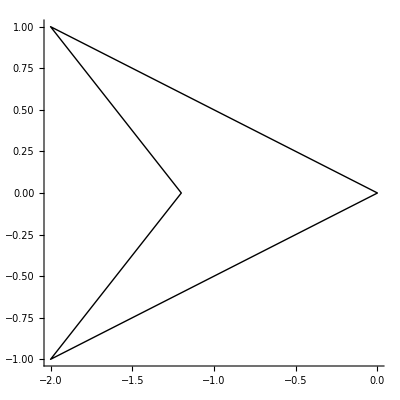

```mathematica
Graphics[Line[ArrowBasic2D],AspectRatio->Automatic,Axes->True]
```

```mathematica
CirclePt[i_]:={-1,0,0}+xrot[i].{0,0,1/3};            (* Revised July 2017 *)
ConePoly[i_]:={CirclePt[i],CirclePt[i+30],{0,0,0}};
HalfDisk=CirclePt/@Range[-90,90,30];
WholeDisk=CirclePt/@Range[0,360,30];
UofSN[S_,N_]:=Transpose[{unit[S],unit[Cross[N,S]],unit[N]}]; (* Rotation matrix that takes (1,0,0) to S and takes (0,0,1) to N.  S and N are orthonormal *)
ShortenForArrow[vector_,ArrowScale_]:=(1-1.02 ArrowScale/length[vector])vector;
```

```mathematica
GraphicsRow[{Graphics3D[{Polygon/@Join[{HalfDisk},ConePoly/@Range[-90,60,30]],
{Red,Polygon[{-1/2,0,0}+zrot[#].{1,1,0}/2&/@Range[90,360,90]]},
{PointSize[.02],Point[{-1,0,-1/3}]}},ViewPoint->5xyztp[{-140,60}]],
Graphics3D[{Polygon/@Join[{WholeDisk},ConePoly/@Range[0,330,30]],
{Red,Polygon[{-1/2,0,0}+zrot[#].{1,1,0}/2&/@Range[90,360,90]]}},ViewPoint->5xyztp[{-140,60}]]}]
```

-Graphics-

```mathematica
Arrow3Dhalf[TipPt_,Direction_,Normal_,ArrowScale_]:={EdgeForm[],Opacity[1],Polygon/@Map[TipPt+ArrowScale*UofSN[Direction,Normal].#&,Join[{HalfDisk},ConePoly/@Range[-90,60,30]],{2}]}; (* Direction and Normal vectors must be perpendicular *)
Arrow3D[TipPt_,Direction_,ArrowScale_]:={EdgeForm[],Opacity[1],Polygon/@Map[TipPt+ArrowScale*ZRot[Theta[Direction]].YRot[-π/2+Phi[Direction]].#&,Join[{WholeDisk},ConePoly/@Range[0,330,30]],{2}]};
```

```mathematica
(*CirclePoint[i_,j_]:=N[j(-{0,0,3}+zrot[i].{1,0,0})]; (* watch out; there is another CirclePoint in the streetlight_parhelia file, for Minnaert cigar *)
ConePoly[i_]:={CirclePoint[i,1],CirclePoint[i+30,1],{0,0,0}};
CenterDisk[v1_,v2_,scale_] :=v2+scale*Transpose[vertical[v2-v1]].(CirclePoint[0,1]+CirclePoint[180,1])/2;
ConeVertex[v1_,v2_,scale_] :=v2+scale*Transpose[vertical[v2-v1]].CirclePoint[0,0];DiskPoly[v1_,v2_,scale_]:=Map[v2+scale*Transpose[vertical[v2-v1]].# &,CirclePoint[#,1]&/@Range[0,360,30]];
ConePolyList[v1_,v2_,scale_]:=Map[v2+scale*Transpose[vertical[v2-v1]].# &,ConePoly/@Range[30,360,30],{2}];
CircleList[v1_,v2_,scale_,j_]:=Map[v2+scale*Transpose[vertical[v2-v1]].CirclePoint[#+30,j] &,Range[0,360,30]];
Arrow3D[v1_,v2_,scale_,tkns_,eye_]:={{EdgeForm[],GrayLevel[1],Polygon/@ConePolyList[v1,v2,scale]},(* sign added April 2011 *)
		                                                                                                      {GrayLevel[1],Polygon[DiskPoly[v1,v2,scale]]},
	                                             {Thickness[tkns],Line[CircleList[v1,v2,scale,#]]&/@Range[0,1,1/7],
	If[False,Line[MapEyeward[#,.01,eye]&/@                     (* may have to adjust eyeward distance here; I took this out March 2011 *){CenterDisk[v1,v2,scale]+scale*unit[Cross[eye-CenterDisk[v1,v2,scale],v2-v1]],ConeVertex[v1,v2,scale],
			      CenterDisk[v1,v2,scale]-scale*unit[Cross[eye-CenterDisk[v1,v2,scale],v2-v1]]}],{}]}};
Arrow3D[v1_,v2_,scale_,tkns_,eye_,1]:={{EdgeForm[],GrayLevel[1],Polygon/@ConePolyList[v1,v2,scale]},(* sign added April 2011 *)
		                                                                                                      {GrayLevel[1],Polygon[DiskPoly[v1,v2,scale]]},
	                                             {Thickness[tkns],Line[CircleList[v1,v2,scale,#]]&/@Range[0,1,1/7],
	If[False,Line[MapEyeward[#,.01,eye]&/@                     (* may have to adjust eyeward distance here; I took this out March 2011 *){CenterDisk[v1,v2,scale]+scale*unit[Cross[eye-CenterDisk[v1,v2,scale],v2-v1]],ConeVertex[v1,v2,scale],
			      CenterDisk[v1,v2,scale]-scale*unit[Cross[eye-CenterDisk[v1,v2,scale],v2-v1]]}],{}]}};
Arrow3D[v1_,v2_,scale_,tkns_,eye_,-1]:=Arrow3D[2v2-v1,v2+3.2scale*unit[v1-v2],scale,tkns,eye,1];
HalfWayIndex[PtList_]:=Sort[{#,PtList[[#]]}&/@Range[Length[PtList]],length[#1[[2]]-(PtList[[1]]+PtList[[-1]])/2]<length[#2[[2]]-(PtList[[1]]+PtList[[-1]])/2]&][[1,1]];
HalfWayArrow[PtList_,ArrowScale_,tkns_,sign_]:=Arrow3D[PtList[[HalfWayIndex[PtList]]],PtList[[HalfWayIndex[PtList]+1]],ArrowScale,.3tkns,eye,sign];*)
```

POINT P ON THE SPHERE IS VISIBLE FROM THE VIEWPOINT EYE IFF SEE[P,EYE].
SEE IS NEEDED FOR LAST EXAMPLE IN NUMERAL FILE.

```mathematica
SeeOnSphere[p_,n_,eye_]:=ScalarProj[p,eye]>n^2/length[eye];
VisibleSegments[SegmentList_,see_]:=Select[SegmentList,see[#⟦1⟧]&&see[#⟦2⟧]&];
ThirdSegments[PointList_]:=SegmentList[PointList]⟦Select[Range[Length[PointList]-1],Mod[#,3]==1&]⟧;
VisibleCurve[PointList_,n_,eye_,tkns_,hue_]:={hue,Thickness[tkns],Line/@VisibleSegments[SegmentList[PointList],SeeOnSphere[#1,n,eye]&]};    (* no longer Graphics3D, May 2012 *)
WholeCurve[PointList_,n_,eye_,ThicknessSolid_,ThicknessDashed_,hue_]:=             (* no longer Graphics3D, May 2012 *){{hue,Thickness[ThicknessDashed],Line/@ThirdSegments[PointList]},{hue,Thickness[ThicknessSolid],Line/@VisibleSegments[SegmentList[PointList],SeeOnSphere[#1,n,eye]&]}};
tpGraphics[v_,eye_,ThicknessSolid_,ThicknessDashed_]:={WholeCurve[zrot[theta[v]].yrot[-#].{1,0,0}&/@Range[0,90sign[v[[3]]],2sign[v[[3]]]],1,eye,ThicknessSolid,ThicknessDashed],
Graphics3D[{Thickness[.9ThicknessSolid],Line[{{0,0,0},xyztp[{theta[v],90}]}]}]};
```

EXAMPLE:

```mathematica
eye=10{3,2,1};Graphics3D[WholeCurve[zrot[#].{1,0,0}&/@Range[0,360,3],1,eye,.003,.002,Red],ViewPoint->eye]
```

-Graphics3D-

FOR DOTTING POLYGONAL CURVES. MAKE SEE = FALSE& TO DOT THE WHOLE THING. NEED VISIBLE SEGMENTS FOR THIS. 
A SEGMENT IS  DELETED IF ONE ENDPOINT FAILS TO SATISFY THE KEEP CONDITION.  MAKE KEEP = TRUE & FOR NO CHANGE.

```mathematica
SubdivisionPoints[{x1_,x2_},tol_]:=(npts=1+3Floor[length[x2-x1]/tol];x1+#/npts(x2-x1)&/@Range[0,npts]);PartitionedSegmentList[{x1_,x2_},tol_]:=SegmentList[SubdivisionPoints[{x1,x2},tol]];
DotLineListVisible[{x1_,x2_},tol_,see_]:=VisibleSegments[SegmentList[SubdivisionPoints[{x1,x2},tol]],see];
DotLineListThird[{x1_,x2_},tol_]                  :=     ThirdSegments[SubdivisionPoints[{x1,x2},tol]];
DotLineListVisible[PointList_,tol_,see_]:=Flatten[Map[DotLineListVisible[#,tol,see] &,SegmentList[PointList]],1];
DotLineListThird[PointList_,tol_]                  :=Flatten[Map[DotLineListThird[#,tol] &,               SegmentList[PointList]],1];
DotLine[PointList_,tol_,see_,keep_,ThicknessSolid_,ThicknessDot_]:={ 
If[ThicknessDot==0,{},{Thickness[ThicknessDot],     Line/@Select[DotLineListThird[PointList,tol],keep[#[[1]]]&&keep[#[[2]]]&]}],
{Thickness[ThicknessSolid],Line/@DotLineListVisible[PointList,tol,see]}         };
```

```mathematica
MinceSegment[{v1_,v2_},tol_]:=(v1+#(v2-v1)/Ceiling[length[v2-v1]/tol])&/@Range[0,Ceiling[length[v2-v1]/tol]];
MinceCurve[PointList_,tol_]:=Flatten[MinceSegment[#,tol]&/@SegmentList[PointList],1];
Redistribute[PointList_,tol_,dashlength_]:=Part[MinceCurve[PointList,tol],Range[1,Length[MinceCurve[PointList,tol]],Round[dashlength/tol]]];
```

A LIST OF SEGMENTS.  LENGTH OF POINTLIST MAKES A DIFFERENCE FOR ENDS OF CURVE. USED FOR CIRCULAR HALOS IN MONTE CARLO.

```mathematica
DotCurveList[PointList_]:=Table[{PointList[[i]],PointList[[i+1]]},{i,1,Length[PointList]-1,3}];
DotCurveList[PointList_,tol_,dashlength_]:=DotCurveList[Redistribute[PointList,tol,dashlength]];
```

NEEDED FOR ATLAS DIAGRAMS, WHOLE SPHERE SIMULATIONS, ORIENTATION DISTRIBUTIONS.

```mathematica
eps3[eye_]:=√(1-1/length[eye]^2)unit[Cross[{0,0,1},eye]];
eps4[eye_]:=√(1-1/length[eye]^2)unit[Cross[eye,eps3[eye]]];
CenterCelSphere[eye_]:=eye/length[eye]^2;
CelSpherePt[t_,eye_]:=CenterCelSphere[eye]+cosd[t] eps3[eye]+sind[t] eps4[eye];
PreCelSphereList[eye_]:=CelSpherePt[#,eye]&/@Range[-90,270];(*Range[0,180]*)
```